```mathematica
fLog [t_,r_,t0_]:= 1/( 1+ (1-1/n)*n * Exp[-r (t-t0)] )
```

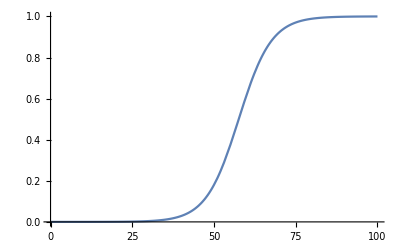

```mathematica
Plot[fLog[t,0.2, 0]/.{n->100000},{t,0,100}]
```

```mathematica
fLog[t_,r_,t0_,a0_]:=1/( 1+ (1- a0)/a0* Exp[-r (t-t0)] )
```

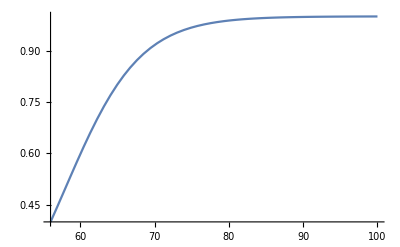

```mathematica
Plot[fLog[t,0.2, 56,0.4]/.{n->100000},{t,56,100}]
```

```mathematica
D[fLog[t,r,t0],t]//FullSimplify
```

(ⅇ^(r (t-t0)) (-1+n) r)/((-1+ⅇ^(r (t-t0))+n)^2)

```mathematica
Integrate[fLog[t,r,t0],t]
```

Log[1-ⅇ^(r (t-t0))-n]/r

```mathematica
Integrate[fLog[tt,r,t0],{tt,t0,t}]//FullSimplify
```

(Log[1-ⅇ^(r (t-t0))-n]-Log[-n])/r

```mathematica
Integrate[fLog[tt,r,0],{tt,0,t}]//FullSimplify
```

(Log[1-ⅇ^(r t)-n]-Log[-n])/r

```mathematica
DSolve[
{
D[1-fLog[t,r,t0],t]b[t]/(1-fLog[t,r,t0])==D[b[t],t],
b[t0]==b0
},
b[t],t]
```

{{b[t]→(b0 n)/(-1+ⅇ^(r (t-t0))+n)}}

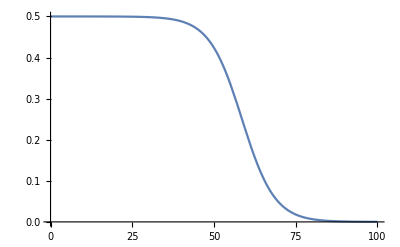

```mathematica
Plot[(b0 n)/(-1+ⅇ^(r (t-t0))+n)/.{b0->0.5, n->100000,r->0.2,t0->1},{t,0,100}]
```

```mathematica
fLog2[t_,r_,t0_,n_]:= n/( 1+ (n-1) * Exp[-r (t-t0)] )
```

```mathematica
Integrate[fLog2[tt,r,0,n],{tt,0,tF}]
```

(n (Log[1-ⅇ^(r tF)-n]-Log[-n]))/r

```mathematica
fLog3[t_,k_, r_]:=k/( 1+(k-1)E^(-r*t) )
```

```mathematica
Solve[99/100 *k==fLog3[tF,k,r],r,Assumptions->{r>0,tF>0,n>1,k>n}]//Simplify
```

{{r→ConditionalExpression[Log[99 (-1+k)]/tF, k>100/99&&n<k]}}

```mathematica
Assuming[λ<0,
DSolve[{x'[t]==λ (1-x[t]) x[t],x[0]==b0},x,t]
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Function[{t},(b0 ⅇ^(t λ))/(1-b0+b0 ⅇ^(t λ))]}}

```mathematica
(b0 ⅇ^(t λ))/(1-b0+b0 ⅇ^(t λ))==b0/(b0+(1-b0)ⅇ^(-t λ))//Simplify
```

True

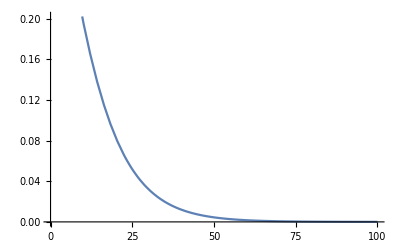

```mathematica
Plot[b0/(b0+(1-b0)ⅇ^(-t λ))/.{b0->0.4,λ->-0.1},{t,0,100}]
```

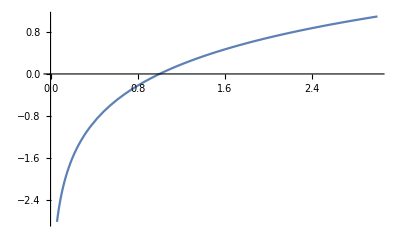

```mathematica
Plot[Log[x],{x,0,3}]
```

```mathematica
dLog1[x_,s_]:=s x(1-x)
```

```mathematica
DSolve[{dLog1[x[t],s]==D[x[t],t],x[0]==1/n},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→ⅇ^(s t)/(-1+ⅇ^(s t)+n)}}

```mathematica
dLog[x_,s_,k_,z_]:=s x(1-x/k-z/(k*s))
(*dLog[x_,s_,k_,z_]:=s x(1-x/k-z/s)*)

dLog[x,s,k,z]
```

s x (1-x/k-z/(k s))

```mathematica
dLog[x_,s_,z_]:=s x(1-x-z/(s))
```

```mathematica
DSolve[{dLog[x[t],s,k,z]==D[x[t],t],x[0]==1/n},x[t],t,Assumptions->{0<x[t]<1,t>0, s ∈Reals,z∈Reals}] // FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→(k s-z)/(s+ⅇ^(-s t+(t z)/k) ((-1+k n) s-n z))}}

```mathematica
DSolve[{dLog[x[t],s,z]==D[x[t],t],x[0]==1/n},x[t],t,Assumptions->{0<x[t]<1,t>0, s ∈Reals,z∈Reals}] // FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→(s-z)/(s+ⅇ^(t (-s+z)) ((-1+n) s-n z))}}

```mathematica
Simplify[(ⅇ^(s t+(k s (ⅈ π- Log[-s+k n s-n z]))/(k s-z)) (k s-z))/(-ⅇ^((t z)/k+(z (ⅈ π- Log[-s+k n s-n z]))/(k s-z))+ⅇ^(s t+(k s (ⅈ π- Log[-s+k n s-n z]))/(k s-z)) s)==(ⅇ^(s t+(ⅈ k s (π+ⅈ Log[-s+k n s-n z]))/(k s-z)) (k s-z))/(-ⅇ^((t z)/k+(ⅈ z (π+ⅈ Log[-s+k n s-n z]))/(k s-z))+ⅇ^(s t+(ⅈ k s (π+ⅈ Log[-s+k n s-n z]))/(k s-z)) s)]
```

True

```mathematica
Simplify[(ⅇ^(s t+(ⅈ s (π+ⅈ Log[-s+n s-n z]))/(s-z)) (s-z))/(-ⅇ^(t z+(ⅈ z (π+ⅈ Log[-s+n s-n z]))/(s-z))+ⅇ^(s t+(ⅈ s (π+ⅈ Log[-s+n s-n z]))/(s-z)) s),Assumptions->{0<x[t]<1,t>0, s ∈Reals,z∈Reals}]
```

(ⅇ^(s (t+(ⅈ (π+ⅈ Log[(-1+n) s-n z]))/(s-z))) (s-z))/(-ⅇ^(z (t+(ⅈ (π+ⅈ Log[(-1+n) s-n z]))/(s-z)))+ⅇ^(s (t+(ⅈ (π+ⅈ Log[(-1+n) s-n z]))/(s-z))) s)

```mathematica
FullSimplify[(k -z/s)/(-ⅇ^((z/k-s)t+((z- k s) (ⅈ π- Log[-s+k n s-n z]))/(k s-z))/s+ 1)==(ⅇ^(s t+(ⅈ k s (π+ⅈ Log[-s+k n s-n z]))/(k s-z)) (k s-z))/(-ⅇ^((t z)/k+(ⅈ z (π+ⅈ Log[-s+k n s-n z]))/(k s-z))+ⅇ^(s t+(ⅈ k s (π+ⅈ Log[-s+k n s-n z]))/(k s-z)) s)]
```

True

```mathematica
Simplify[(k -z/s)/(ⅇ^((z/k-s)t) n(k-1/n - z/s)+ 1)==(k s-z)/(-ⅇ^((z/k-s)t+((ⅈ z-ⅈ k s) (π+ⅈ Log[-s+k n s-n z]))/(k s-z))+ s)]
```

True

```mathematica
Simplify[(s-z)/(-ⅇ^((z-s)t +(z-s)(ⅈ π- Log[(-1+n) s-n z])/(s-z))+ s)==(s-z)/(-ⅇ^((z-s) (t+(ⅈ (π+ⅈ Log[(-1+n) s-n z]))/(s-z)))+ s)]
```

True

```mathematica
Simplify[(1-z/s)/(-ⅇ^(-(s-z)t +ⅈ π)(n(1-z/s)-1)+ 1)==(s-z)/(-ⅇ^((z-s)t +(z-s)(ⅈ π- Log[(-1+n) s-n z])/(s-z))+ s)]
```

True

```mathematica
Simplify[(1-z/s)/(ⅇ^(-(s-z)t)(n(1-z/s)-1)+ 1)==(s-z)/(-ⅇ^((z-s)t +(z-s)(ⅈ π- Log[(-1+n) s-n z])/(s-z))+ s)]
```

True

```mathematica
(1-z/s)/(1+(n(1-z/s)-1)ⅇ^(-(s-z)t))
```

(1-z/s)/(1+ⅇ^(t (-s+z)) (-1+n (1-z/s)))

```mathematica
Simplify[(k -z/s)/(1+(k-1/n - z/s)n ⅇ^(-(s-z/k)t))==(k s-z)/(s+ⅇ^(-s t+(t z)/k) ((-1+k n) s-n z))]
```

True

```mathematica
(*fAdLog[t_]:=(k -z/s)/(1+(k-x0 - z/s)/x0 ⅇ^(-(s-z/k)t))*)
fAdLog[t_]:=((k -z/s)ⅇ^((s-z/k)t))/(ⅇ^((s-z/k)t)+(k-x0 - z/s)/x0)
```

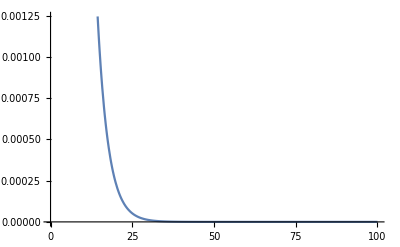

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[t]→ⅇ^(a t)/(-1+ⅇ^(a t)+n)}}

```mathematica
Plot[fAdLog[t]/.{k->0.5,s->0.1,z->0.2,x0->0.1},{t,0,100}]
```

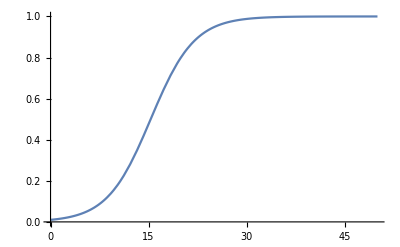

```mathematica
Plot[y[t]/.{{y[t]->ⅇ^(a t)/(-1+ⅇ^(a t)+n)}}/.{a->0.3,n->100},{t,0,50}]
```

## Competition analytics

### Expected Growth, Identical fitness

```mathematica
yComp[t_]=y[t]/.DSolve[{(a y[t]+μ/n)(1-y[t])==D[y[t],t],y[0]==0},y[t],t][[1]]//FullSimplify;
yComp[t+u]
```

1-(a n+μ)/(a n+ⅇ^((t+u) (a+μ/n)) μ)

```mathematica
xComp[t_,u_]=x[t]/.DSolve[{D[x[t],t]==a x[t](1-yComp[t]),x[u]==1/n},x[t],t][[1]]//FullSimplify
```

(ⅇ^(((t-u) (a n+μ))/n) (a n+ⅇ^(u (a+μ/n)) μ))/(n (a n+ⅇ^(t (a+μ/n)) μ))

```mathematica
Plot[
{yComp[t]/.{a->0.1,n->200000,μ->5.12},
xComp[t,1]/.{a->0.1,n->200000,μ->5.12},
xComp[t,5]/.{a->0.1,n->200000,μ->5.12},
xComp[t,10]/.{a->0.1,n->200000,μ->5.12}},
{t,0,100},PlotRange->Full,PlotLabels->{"total variant fraction","u=1","u=5", "u=10"},
AxesLabel->{t,x}]
```

-Graphics-

### Expected Growth, Individual fitness with averaged competition

```mathematica
xCompIndFit[t_,u_]=x[t]/.DSolve[{D[x[t],t]==s x[t](1-a/s yComp[t]),x[u]==1/n},x[t],t][[1]]//FullSimplify
```

(ⅇ^(((t-u) (n s+μ))/n) (a n+ⅇ^(u (a+μ/n)) μ))/(n (a n+ⅇ^(t (a+μ/n)) μ))

```mathematica
xComp[t,3]
xCompIndFit[t,3]
```

(ⅇ^(((-3+t) (a n+μ))/n) (a n+ⅇ^(3 (a+μ/n)) μ))/(n (a n+ⅇ^(t (a+μ/n)) μ))

(ⅇ^(((-3+t) (n s+μ))/n) (a n+ⅇ^(3 (a+μ/n)) μ))/(n (a n+ⅇ^(t (a+μ/n)) μ))

```mathematica
With[{aa=0.2,u=5,m=1},
Plot[
{
(*yComp[t]/.{a->0.2,n->200000,μ->1},*)
xCompIndFit[t,u]/.{s->aa,a->aa,n->200000,μ->m},
xCompIndFit[t,u]/.{s->aa-(0.08*aa),a->aa,n->200000,μ->m},
xCompIndFit[t,u]/.{s->aa+(0.08*aa),a->aa,n->200000,μ->m}},
{t,0,100},PlotLabels->{"s=a","s<a","s>a"}]
]
```

-Graphics-

```mathematica
yTAdj[t_]:=y[t]/.{y[t]->1-(a n+μ)/(a n+ⅇ^(t (a+μ/n)) μ)}
yTAdjAv[t_]:=y[t]/.{y[t]->1-(s n+μ)/(s n+ⅇ^(t (s+μ/n)) μ)}
yTAdjCond[t_]:=y[t]/.{y[t]->1-(-1+n)/(-1+ⅇ^(t (a+μ/n))+n)}
yTAdj[t+u]
yTAdjCond[t+u]
yTAdjAv[t+u]
```

1-(a n+μ)/(a n+ⅇ^((t+u) (a+μ/n)) μ)

1-(-1+n)/(-1+ⅇ^((t+u) (a+μ/n))+n)

1-(n s+μ)/(n s+ⅇ^((t+u) (s+μ/n)) μ)

```mathematica
D[x[t],t]==a x[t](1-yTAdjAv[t])
```

x'[t]==(a (n s+μ) x[t])/(n s+ⅇ^(t (s+μ/n)) μ)

```mathematica
DSolve[{D[x[t],t]==a x[t](1-yTAdjAv[t]),x[u]==1/n},x[t],t]//FullSimplify
```

{{x[t]→(ⅇ^((a ((t-u) (n s+μ)-n Log[n s+ⅇ^(t (s+μ/n)) μ]+n Log[n s+ⅇ^(u (s+μ/n)) μ]))/(n s)))/n}}

```mathematica
exprAd=D[x[t],t]==a x[t]*(1-y[t])/.ySolAdj
```

ReplaceAll::reps: {ySolAdj} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x'[t]==a x[t] (1-y[t])/.ySolAdj

```mathematica
solCompAdj=DSolve[{exprAd,x[0]==1/n},x[t],t]//FullSimplify
```

{{x[t]→(a n+μ)/(n (a ⅇ^(-t (a+μ/n)) n+μ))}}

```mathematica
Simplify[(a n+μ)/(n (a ⅇ^(-t (a+μ/n)) n+μ))==(1/n+a/μ)/(a/μ n ⅇ^(-t a(1 +μ/(a n))) +1)]
```

True

```mathematica
solCompAdjU=DSolve[{D[x[t],t]==a x[t]*(1-yTAdj[t]),x[u]==1/n},x[t],t]//FullSimplify
```

{{x[t]→(ⅇ^(((t-u) (a n+μ))/n) (a n+ⅇ^(u (a+μ/n)) μ))/(n (a n+ⅇ^(t (a+μ/n)) μ))}}

```mathematica
Simplify[(ⅇ^(((t-u) (a n+μ))/n) (a n+ⅇ^(u (a+μ/n)) μ))/(n (a n+ⅇ^(t (a+μ/n)) μ))==(1/n+ⅇ^(-u (a+μ/n))a/μ)/(1+a/μ n ⅇ^(-t (a+μ/n)))]
```

True

```mathematica
yTAdjCond[t]
```

1-(-1+n)/(-1+ⅇ^(t (a+μ/n))+n)

```mathematica
Plot[{
(*x[t]/.solNoComp/.{a->0.2,n->100000,μ->5},*)
(*x[t]/.solComp/.{a->0.2,n->100000,μ->1},*)
x[t]/.solCompAdj/.{a->0.17,n->100000,μ->1},
x[t]/.solCompAdjU/.{a->0.17,n->100000,μ->1,u->5},
x[t]/.solCompAdjU/.{a->0.17,n->100000,μ->1,u->10},
(*(ⅇ^((a ((t-u) (n s+μ)-n Log[n s+ⅇ^(t (s+μ/n)) μ]+n Log[n s+ⅇ^(u (s+μ/n)) μ]))/(n s)))/n/.{a->0.16,s->0.21,n->100000,μ->1,u->0},*)
(*x[t]/.solCompAdjCondU/.{a->0.17,n->100000,μ->1, u->0}*)
},{t,0,100},PlotRange->Full,PlotLabels->{"u=0","u=5","u=10","individual fitness"}]
```

-Graphics-

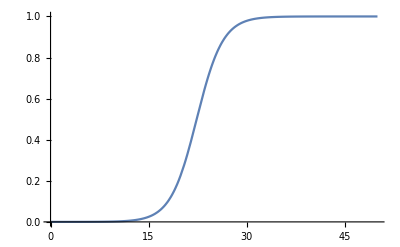

```mathematica
Plot[{
(*y[t]/.ySol/.{a->0.4,n->100000,μ->0.7},*)
y[t]/.ySolAdj/.{a->0.5,n->100000,μ->0.7},
(*y[t]/.ySolAdjCond/.{a->0.4,n->100000,μ->0.7}*)
},{t,0,50}]
```

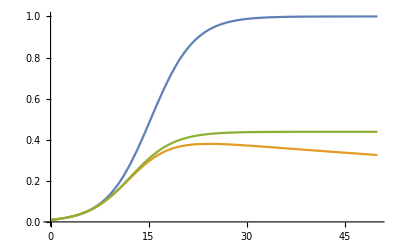

```mathematica
Plot[{
x[t]/.solNoComp/.{a->0.3,n->100,μ->0.7},
x[t]/.solComp/.{a->0.3,n->100,μ->0.7},
x[t]/.solCompAdj/.{a->0.3,n->100,μ->0.7}

},{t,0,50}]
```

## Separate average and individual fitness

```mathematica
ySolAdj=DSolve[{(α a y[t]+μ/n)(1-y[t])==D[y[t],t],y[0]==0},y[t],t][[1]]//FullSimplify
```

{y[t]→1-(a n α+μ)/(a n α+ⅇ^((t (a n α+μ))/n) μ)}

```mathematica
α s x[t](1-(a/s)y[t])/.ySolAdj
```

s α (1-(a (1-(a n α+μ)/(a n α+ⅇ^((t (a n α+μ))/n) μ)))/s) x[t]

```mathematica
solCompAdjInd=DSolve[{D[x[t],t]==α s x[t](1-(a/s)y[t])/.ySolAdj,x[u]==1/n},x[t],t][[1]]//FullSimplify
```

{x[t]→(ⅇ^(((t-u) (n s α+μ))/n) (a n α+ⅇ^((u (a n α+μ))/n) μ))/(n (a n α+ⅇ^((t (a n α+μ))/n) μ))}

```mathematica
solCompAdj
```

{{x[t]→(a n+μ)/(n (a ⅇ^(-t (a+μ/n)) n+μ))}}

```mathematica
With[{aa=1.5},
Plot[{
x[t]/.solCompAdj/.{a->aa,n->100000,μ->1},
x[t]/.solCompAdjInd/.{α->1, a->aa,s->aa-(0.1*aa),n->200000,μ->1,u->0},
(*x[t]/.solCompAdjCondU/.{a->0.17,n->100000,μ->1, u->0}*)
},{t,0,150},PlotRange->Full,PlotLabels->{"u=0","individual fitness"}]
]
```

-Graphics-

```mathematica
Simplify[(ⅇ^(-α (a-s)(t-u)) (ⅇ^(-( α a+μ/n)u) a α+  μ/n))/(n (a α ⅇ^(-(a α+μ/n)t)+ μ/n))==(ⅇ^(((t-u) (n s α+μ))/n) (a n α+ⅇ^((u (a n α+μ))/n) μ))/(n (a n α+ⅇ^((t (a n α+μ))/n) μ))]
```

True

```mathematica
x[t]/.solCompAdjU
```

(ⅇ^(((t-u) (n s α+μ))/n) (a n α+ⅇ^((u (a n α+μ))/n) μ))/(n (a n α+ⅇ^((t (a n α+μ))/n) μ))

## Expression rewrites

```mathematica
Simplify[yComp[t]==1-(1+μ/(n a))/(1+μ/(n a)ⅇ^(t (a+μ/n)))]
```

True

```mathematica
Simplify[((ⅇ^(-α (a-s)(t-u)) (ⅇ^(-( α a+μ/n)u) a α+  μ/n))/(n (a α ⅇ^(-(a α+μ/n)t)+ μ/n))/.{α->1})==xCompIndFit[t,u]]
```

True

```mathematica
Simplify[xCompIndFit[t,u]==(ⅇ^(((t-u) (n s+μ))/n) (a+ⅇ^(u (a+μ/n)) μ/n))/(n (a+ⅇ^(t (a+μ/n)) μ/n))]
```

True